```mathematica
eta[t_]:=c4/(Cos[c1 t+c2]);
x[t_]:=c4 Tan[c2+c1 t]+c3;
```

```mathematica
(*Check eom satisfied: should give constants*)
Px=D[x[t],t]/(H^2 eta[t]^2 ) (*linear momentum in the x-direction along the particle's trajectory*)
En=-(eta[t]D[eta[t],t]-x[t]D[x[t],t])/(H^2 eta[t]^2)//Simplify (*(de Sitter) energy along the particle's trajector*)
CQ={Px,En}; (*constants of motion*)
H=1;
dsConstEta= ((Integrate[D[x[t],t]/(-H eta[t]),t]/.t->1)-(Integrate[D[x[t],t]/(-H eta[t]),t]/.t->0))//FullSimplify;(*geodesic distance for eta=constant*)
```

c1/c4

(c1 c3)/c4

```mathematica
(*check original eom*)
D[eta[t],{t,2}]-(D[eta[t],t]^2+D[x[t],t]^2)/eta[t]//Simplify
D[x[t],{t,2}]-2 D[eta[t],t]D[x[t],t]/eta[t]
```

0

0

```mathematica
solconst=Solve[{eta[0]==EA,eta[1]==EB,x[0]==XA,x[1]==XB},{c1,c2,c3,c4}]/.{C[1]->0,C[2]->0}//Simplify;
```

```mathematica
solINI=Simplify[solconst,XB>XA>0&&EA<EB<0]
```

{{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→-(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]},{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]}}

```mathematica
par={EA->-5,EB->-5,XA->1,XB->10};
solINI/.par//N
{Re[x[t]/.solINI⟦1⟧/.par],Re[eta[t]/.solINI⟦1⟧/.par]}/.t->0.5
{Im[x[t]/.solINI⟦1⟧/.par],Im[eta[t]/.solINI⟦1⟧/.par]}/.t->0.5
CQ/.solINI⟦1⟧/.par//N
dsConstEta/.solINI⟦1⟧/.par//N
```

{{c3→5.5,c4→2.17945,c1→2.23954,c2→2.02182},{c3→5.5,c4→-2.17945,c1→-2.23954,c2→1.11977}}

{5.5,-2.17945}

{0,0}

{1.02757,5.65164}

2.94444

```mathematica
sol1=Solve[(solINI[[1,2,2]]/.{EA->EB})==0,XB]
```

{{XB→-2 EB+XA},{XB→2 EB+XA}}

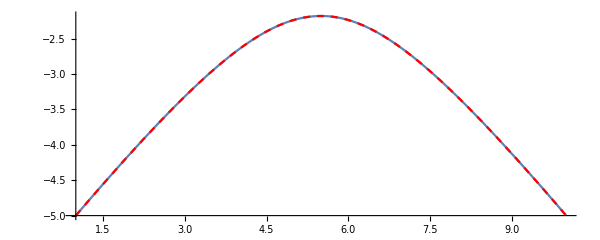

```mathematica
Show[ParametricPlot[{Re[x[t]/.solINI⟦1⟧/.par],Re[eta[t]/.solINI⟦1⟧/.par]},{t,0,1}],
ParametricPlot[{Re[x[t]/.solINI⟦2⟧/.par],Re[eta[t]/.solINI⟦2⟧/.par]},{t,0,1},PlotStyle->{Red, Dashed}],ImageSize->600]
```

## sqrt action from n-action

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
(*Relativistic particle in flat spacetime*)
L=m/(2 n)(-T'[s]^2+X'[s]^2)+(m n)/2;
```

```mathematica
soln=Solve[D[L,n]==0,n]
```

{{n→-√(-T'[s]^2+X'[s]^2)},{n→√(-T'[s]^2+X'[s]^2)}}

```mathematica
Simplify[L/.soln⟦1⟧]
```

-m √(-T'[s]^2+X'[s]^2)

```mathematica
(*Relativistic particle in de Sitter spacetime*)
LdS=m/(2 n  Hub^2 η[s]^2)(-η'[s]^2+X'[s]^2)+(m n)/2;
solndS=Solve[D[LdS,n]==0,n]
LdSsqrt=Simplify[LdS/.solndS] (*note that the second sol for N yields the wrong sign for the action*)
```

{{n→-(√(X'[s]^2-η'[s]^2))/(Hub η[s])},{n→(√(X'[s]^2-η'[s]^2))/(Hub η[s])}}

{-(m √(X'[s]^2-η'[s]^2))/(Hub η[s]),(m √(X'[s]^2-η'[s]^2))/(Hub η[s])}

```mathematica
EulerEquations[LdS,η[s],s]//Simplify
EulerEquations[LdSsqrt[[1]],η[s],s]//Simplify

EulerEquations[LdS,X[s],s]//Simplify
EulerEquations[LdSsqrt[[1]],X[s],s]//Simplify
```

(m (X'[s]^2+η'[s]^2-η[s] η''[s]))/(Hub n η[s])==0

(m X'[s] (X'[s]^3+η[s] η'[s] X''[s]-X'[s] (η'[s]^2+η[s] η''[s])))/(Hub η[s] √(X'[s]^2-η'[s]^2))==0

(m (-2 X'[s] η'[s]+η[s] X''[s]))/(Hub n η[s])==0

(m η'[s] (X'[s]^3+η[s] η'[s] X''[s]-X'[s] (η'[s]^2+η[s] η''[s])))/(Hub η[s]^2 (X'[s]^2-η'[s]^2)^(3/2))==0